```mathematica
myFactorial[n_Integer]:=n!;
myFactorial[n_]:=Infinity;
mnlfac[nn_,n_,a_List]:=Product[((nn+2*k)!)/(2^(2*k)*myFactorial[((nn+a[[k+1]]+2*n-1)/2)]*myFactorial[((nn-a[[k+1]]+2*n-1)/2)]),{k,0,n-1}]*Product[(a[[i]])^2,{i,1,n}]*Product[((a[[i]])^2-(a[[j]])^2)^2,{i,1,n},{j,i+1,n}]*2^(-n^2+2*n-n*nn)*n!/(Product[(2*i)!,{i,1,n}]);
findmax[n_,nn_]:=Module[{a=Table[2*(n-i)+1+Mod[nn,2],{i,n}],i,oldval,newval,cont=True},
While[cont,
cont=False;
For[i=n,i≥1,i--,
oldval=mnlfac[nn,n,a];
a[[i]]+=2;
newval=mnlfac[nn,n,a];
While[newval>oldval,
cont=True;
oldval=newval;
a[[i]]+=2;
newval=mnlfac[nn,n,a]];
a[[i]]-=2;
]
];
a];
rhotheor[x_,c_]:=(1-Sign[Abs[x]-c/2])/2*Re[(1-Sign[c-4])/4+Sign[c-4]*1/(4*Pi)*(ArcTan[(-8-c (-4+x))/(√((-4+c)^2) √(-4+2 c-x^2))]+ArcTan[(-8+c (4+x))/(√((-4+c)^2) √(-4+2 c-x^2))])];
rhotheor2[x_,c_]:=(1-Sign[Abs[x]-c/2])/2*((1-Sign[c-4])/4+-Sign[c-4]/(4*Pi)*(Im[Log[Sqrt[(c-4)^2]*Sqrt[x^2-2*c+4]-c*(x-4)-8]+Log[Sqrt[(c-4)^2]*Sqrt[x^2-2*c+4]+c*(x+4)-8]]-Pi));
ft[y_,c_]:=1+NIntegrate[1-4*rhotheor[x,c],{x,0,y}];
prepdata[bntab_]:=Module[{n},n=Length[bntab];Table[bntab[[i]]-(2*(n-i)+1),{i,n}]];
trtab[tab_]:=Table[Length[Select[tab,#≥i&]],{i,tab[[1]]}];
reccolumn[colnum_,n_,wd_,sc_:1]:=Table[Rectangle[sc*{colnum,i-1},sc*{colnum+wd,i}],{i,n}];showbntableau[tab_,sc_:1,rot_:False,tran_:{0,0}]:=If[tab=={0},Graphics[Text[Style["∅",FontSize->16]],ImageSize->16],
Module[{tab1},
tab1=Append[Table[tab[[-1]]+(tab[[i]]-tab[[-1]])/2,{i,1,Length[tab]-1}],tab[[-1]]];Graphics[{White,EdgeForm[Thin],
Translate[
If[rot,Rotate[#,Pi/4,{0,0}],#]&/@
Flatten[
Table[reccolumn[If[i≤tab1[[-1]],i/2-1/2,i-tab1[[-1]]/2-1],trtab[tab1][[i]],If[i≤tab1[[-1]], 1/2,1],sc],{i,Length[trtab[tab1]]}],3],
tran]
}]]];
showDiagramAndLimitShape[n_,nn_]:=Module[{data,cc},
cc=(nn+2*n-1)/n;
data=findmax[n,nn];
Show[showbntableau[prepdata[data],Sqrt[2]/n,True,{1,0}],
Plot[ft[x,cc],{x,0,cc/2+1/2}],
Plot[-x+1,{x,0,1},PlotStyle->Gray],Plot[x-1,{x,1,cc/2},PlotStyle->Gray],AspectRatio->1,PlotRange->{{0,cc/2+1/2},{0,cc/2+1/2}},Axes->True]];
```

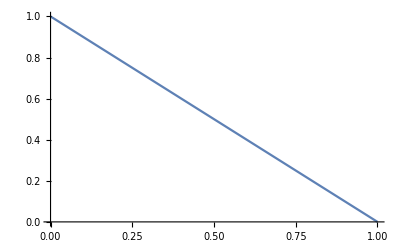

```mathematica
Plot[ft[x,2.0001],{x,0,1}]
```

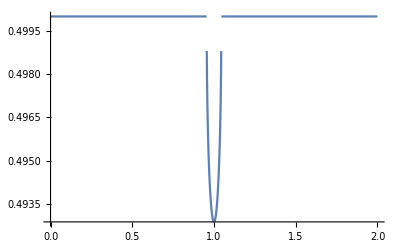

```mathematica
Plot[rhotheor[y-1,2.001],{y,0,2}]
```

```mathematica
glft[y_,cc_]:=1+NIntegrate[1-2*rhotheor[yy-(cc+1)/2,cc+1],{yy,0,y}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in yy near {yy} = {0.0000204279}. NIntegrate obtained 0. and 0. for the integral and error estimates.

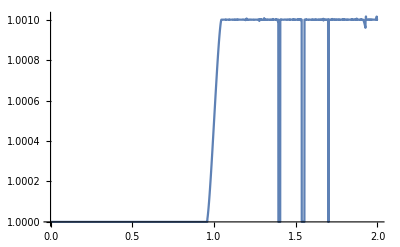

```mathematica
Plot[glft[y,1.001],{y,0,2}]
```

```mathematica
Plot[rhotheor[yy+(3+1)/2,3+1],{yy,0,5}]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

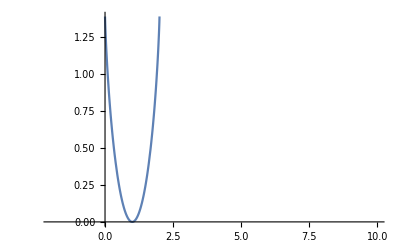

```mathematica
Plot[(y*Log[y]+(cc+1-y)*Log[cc+1-y])/.{cc->1},{y,-2,10}]
```

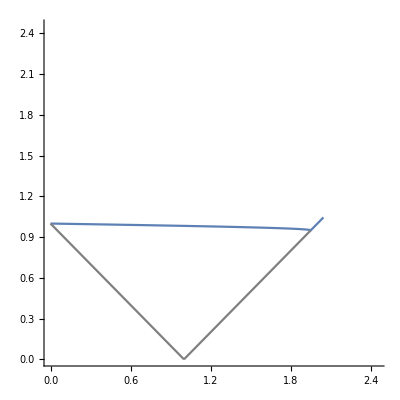

```mathematica
showDiagramAndLimitShape[10,20]
```